```mathematica
(* << Statistics`ContinuousDistributions` *)
```

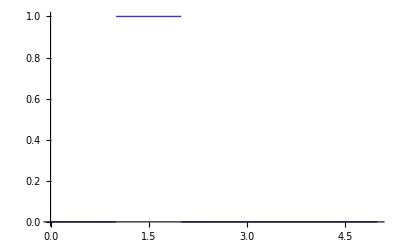

```mathematica
distuni=UniformDistribution[{1,2}];
Plot[PDF[distuni,x],{x,0,5}]
```

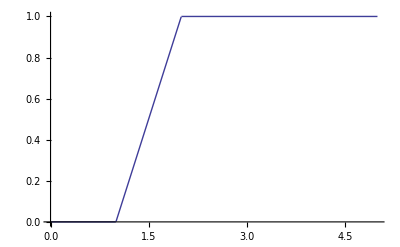

```mathematica
Plot[CDF[distuni,x],{x,0,5}]
```

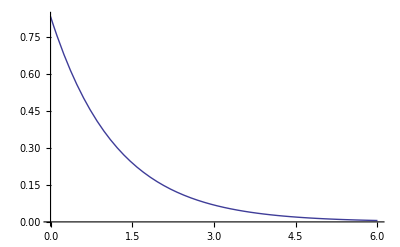

```mathematica
distexp=ExponentialDistribution[1/1.2];
Plot[PDF[distexp,x],{x,0,6}]
```

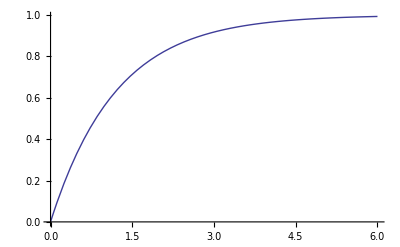

```mathematica
Plot[CDF[distexp,x],{x,0,6}]
```

x^n is: {0.46381,0.430739,0.398067,0.392013,1.06805,1.2725,2.52819,0.0225765,0.839123,0.126871,1.54356,0.406105,0.741868,0.479353,2.36027}, where n=15

The sum is: 13.0731

ML β is: 0.871539

ML probability is: 2.40591×10^-6

Aposteriori prob is: 3.18022×10^-7

Gaussian variance: 19.7477

Gaussian approx. prob.: 2.1939×10^-8

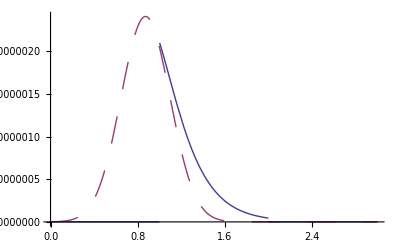

```mathematica
n=15;
xn=RandomReal[distexp,n];
Print["\!\(\*SuperscriptBox[\(x\), \(n\)]\) is: ",xn,", where n=",n];
sumxn=Plus@@xn;Print["The sum is: ",sumxn];
mlbeta=sumxn/n;Print["ML β is: ",mlbeta];
prmlxn=(1/mlbeta)^n ⅇ^-n;
Print["ML probability is: ",prmlxn];
seqpr=∫_1^2 ⅇ^(-sumxn/b)/b^n ⅆb;
Print["Aposteriori prob is: ",seqpr];
gaussianA=n^3/sumxn^2;
Print["Gaussian variance: ",gaussianA];
prapprox=√((2 π)/n^3) sumxn (sumxn/n)^n ⅇ^-n;
Print["Gaussian approx. prob.: ",prapprox];
f[b_]:=(ⅇ^(-sumxn/b) PDF[distuni,b])/b^n;
g[b_]:=prmlxn ⅇ^(1/2 (-n) (b/mlbeta-1)^2);
Plot[{f[b],g[b]},{b,0,3},PlotRange->All,PlotStyle->{{},{Dashing[{0.05,0.05}]}}]
```